## Interraction of two bar magnets

-Graphics-

```mathematica
Fmagn[x_]:= (B0^2 A^2(L^2+R^2))/(π μ0 L^2)(1/x^2+1/(x+2L)^2-2/(x+L)^2)
```

```mathematica
μ0 = 1.26*10^-6;
B0 = 0.3;
R = 13.05/2*10^-3;
A = π R^2;
L = 6.55*10^-3; 
m = 7.75*10^-3 ; (*mass of the magnet*)
l = 0.24; (*distance between the magnet and the rotational origin*)
```

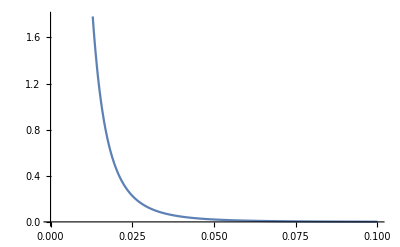

```mathematica
Plot[Fmagn[x],{x, 0, 0.1}]
```

## Force of a leaf spring

## -Graphics-

## q1 = 4 for rectangular spring

## -Graphics-

```mathematica
Fspring[s_]:=(b Em h^3 s)/(Ls^3 4)
```

```mathematica
Ls = 0.25;
h = 0.6*10^-3;
b=2.8*10^-2;
Em = 100*10^9;
M = (150.74*10^-3)/1.03*Ls; (*mass of the oscillating part of the ruler*)
```

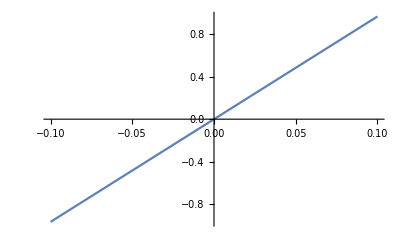

```mathematica
Plot[Fspring[x], {x, -0.1, 0.1}]
```

```mathematica
Inertia = (M Ls^2)/3+m l^2
```

0.00120864

```mathematica
xLeft0 = -0.1;
xRight0 = -0.0;
```

```mathematica
solution = NDSolve[{xLeft[0] == -0.14, xRight[0] == xRight0, xRight'[0] == 0, xLeft'[0] == 0,xRight''[t]/l == -(Fspring[xRight[t]-xRight0] * Ls)/Inertia+ (Fmagn[xRight[t] - xLeft[t]]*l)/Inertia, 
xLeft''[t]/l == -(Fspring[xLeft[t]-xLeft0]*Ls)/Inertia-(Fmagn[xRight[t] - xLeft[t]]*l)/Inertia},
 {xLeft[t], xRight[t]},{t, 0, 20}]
```

{{xLeft[t]→InterpolatingFunction[…][t],xRight[t]→InterpolatingFunction[…][t]}}

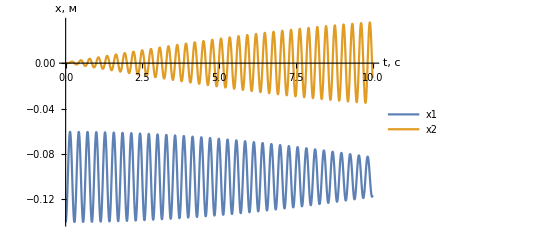

```mathematica
combPlot = Plot[{solution[[1,1, 2]], solution[[1,2, 2]](*, solution[[1,1, 2]] - solution[[1,2, 2]]*)}, {t, 0, 10}, AxesLabel->{"t, с", "x, м"}, AxesStyle->Directive[Black, 12], PlotLegends->{"x1", "x2", "x1-x2"}]
```

## Combination of different modes

```mathematica
solutionInPhase = NDSolve[{xLeft[0] == -0.10+0.027, xRight[0] == -0.00+0.027, xRight'[0] == 0, xLeft'[0] == 0,xRight''[t]/l == -(Fspring[xRight[t]-xRight0] * Ls)/Inertia+ (Fmagn[xRight[t] - xLeft[t]]*l)/Inertia, 
xLeft''[t]/l == -(Fspring[xLeft[t]-xLeft0]*Ls)/Inertia-(Fmagn[xRight[t] - xLeft[t]]*l)/Inertia},
 {xLeft[t], xRight[t]},{t, 0, 20}];
solutionAntiPhase = NDSolve[{xLeft[0] == -0.10+0.027, xRight[0] == +0.00-0.027, xRight'[0] == 0, xLeft'[0] == 0,xRight''[t]/l == -(Fspring[xRight[t]-xRight0] * Ls)/Inertia+ (Fmagn[xRight[t] - xLeft[t]]*l)/Inertia, 
xLeft''[t]/l == -(Fspring[xLeft[t]-xLeft0]*Ls)/Inertia-(Fmagn[xRight[t] - xLeft[t]]*l)/Inertia},
 {xLeft[t], xRight[t]},{t, 0, 20}]
```

{{xLeft[t]→InterpolatingFunction[…][t],xRight[t]→InterpolatingFunction[…][t]}}

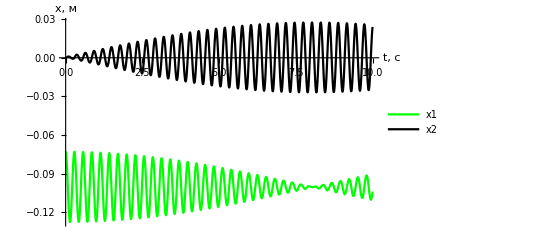

```mathematica
Plot[{solutionInPhase[[1,1, 2]], solutionInPhase[[1,2, 2]]}, {t, 0, 1}, AxesLabel->{"t, с", "x, м"}, AxesStyle->Directive[Black, 12], PlotLegends->{"x1", "x2"}];
Plot[{solutionAntiPhase[[1,1, 2]], solutionAntiPhase[[1,2, 2]]}, {t, 0, 1}, AxesLabel->{"t, с", "x, м"}, AxesStyle->Directive[Black, 12], PlotLegends->{"x1", "x2"}];
assembledCombPlot = Plot[{(solutionInPhase[[1,1,2]] + solutionAntiPhase[[1,1,2]])/2, (solutionInPhase[[1,2,2]] + solutionAntiPhase[[1,2,2]])/2}, {t, 0, 10}, AxesLabel->{"t, с", "x, м"}, AxesStyle->Directive[Black, 12], PlotLegends->{"x1", "x2"}, PlotStyle->{Green, Black} ]
```

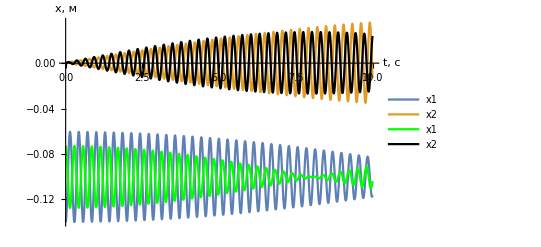

```mathematica
Show[combPlot, assembledCombPlot]
```

## It does not work!